Evaluation>Evaluate Notebook

```mathematica
$H="/Volumes/World/Users/latur/Public/DREAM6/r-code/";
FN[pattern_]:=FileNames[pattern,$H<>"results/",2];
```

```mathematica
(* Чтение файла известных параметров, преобразование в список *)
P=StringCases[
StringReplace[Import[#],"\n"->","],
RegularExpression["=([0-9.]{1,10})"]->"$1"
]&/@FileNames["parms.txt",$H,∞]//ToExpression;
```

```mathematica
(* График значений функционала *)
FValue[list_]:={#⟦1⟧,#⟦3⟧}&/@list;
```

```mathematica
(* График значений расстояния между параметрами *)
Distance[pred_,real_]:=Total[Log[pred/real⟦1;;Length[pred]⟧]^2]/Length[pred];
PValue[list_,p_]:={#⟦1⟧,Distance[#⟦4;;-1⟧,p]}&/@list;
```

```mathematica
LP[list_,prange_]:=ListPlot[ list,Frame->True,Mesh->All,Joined->True,PlotRange->prange,ImageSize->350];
Vi[e_,p_]:=Grid[{{LP[FValue/@e,{{-10,800},{-10,250}}],LP[PValue[#,p]&/@e,{{-10,800},{-1,10}}]}}];
```

Здесь и далее: слева значение минимизируемого функционала, справа расстояние до известных параметров. 
Структура имён файлов: m1p150e2, m1 — модель (1), p150 — размер популяции (150), e2 — es_lambda (2)

#### Размер популяции (150) фиксирован, es_lambda = 2, 15, 45.

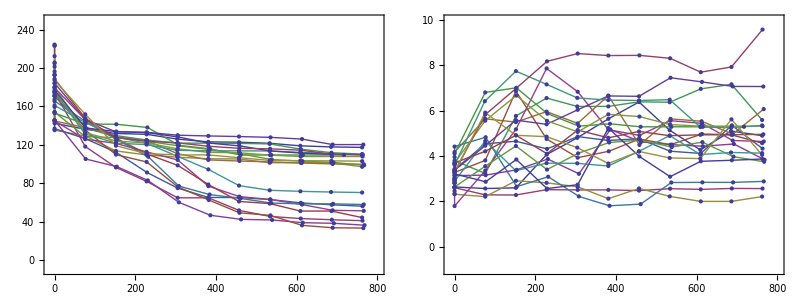

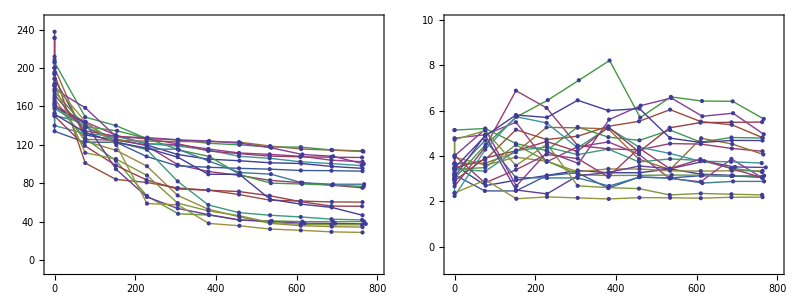

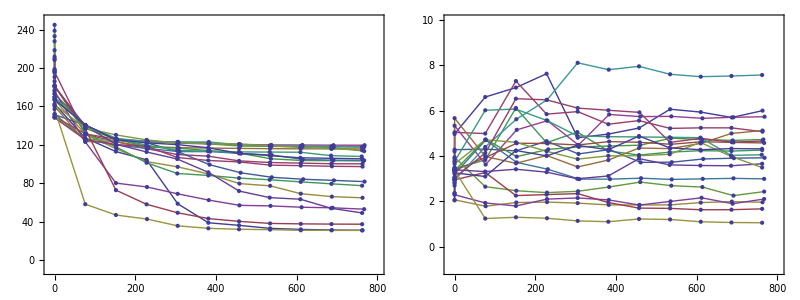

```mathematica
Vi[Import/@FN["*m1p150e2*.dev"],P⟦1⟧]
Vi[Import/@FN["*m1p150e15*.dev"],P⟦1⟧]
Vi[Import/@FN["*m1p150e45*.dev"],P⟦1⟧]
```

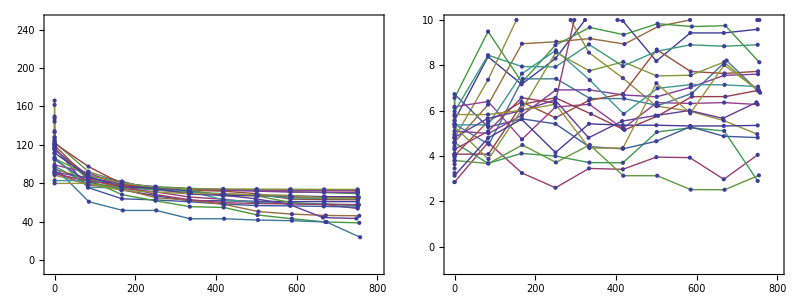

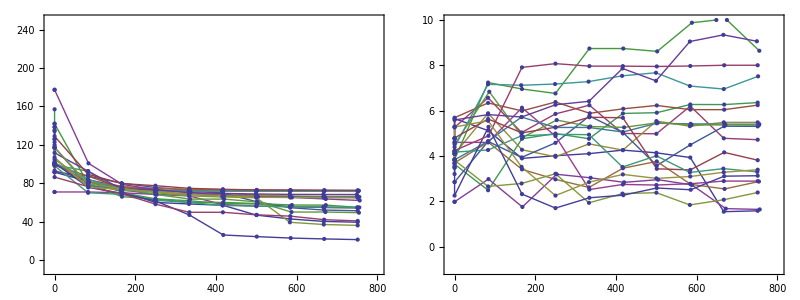

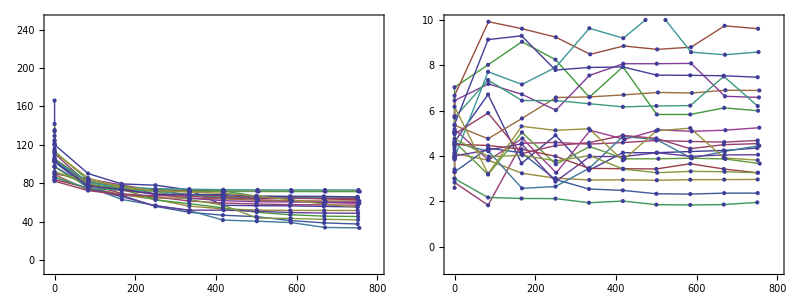

```mathematica
Vi[Import/@FN["*m2p150e2*.dev"],P⟦2⟧]
Vi[Import/@FN["*m2p150e15*.dev"],P⟦2⟧]
Vi[Import/@FN["*m2p150e45*.dev"],P⟦2⟧]
```

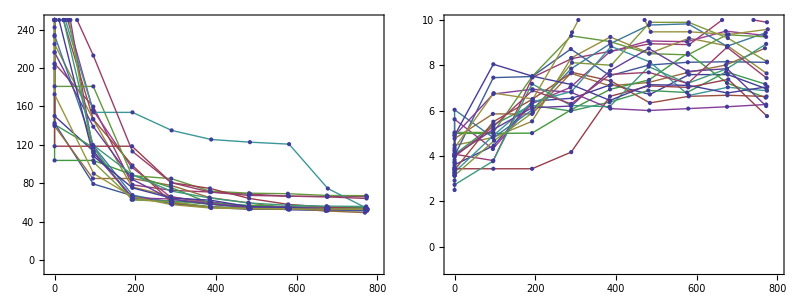

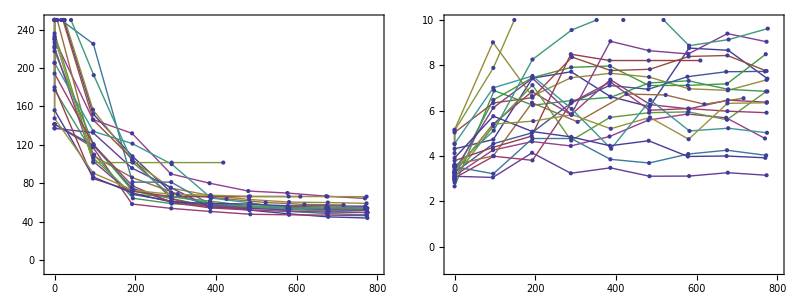

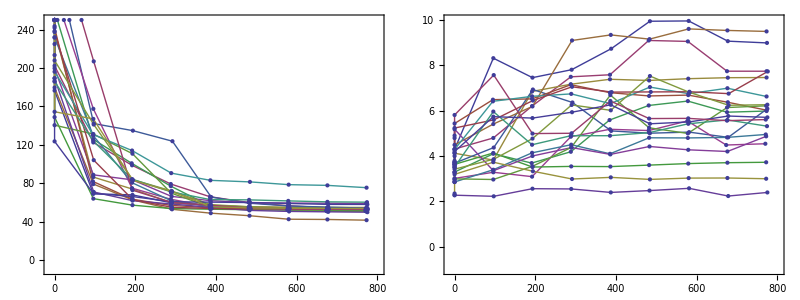

```mathematica
Vi[Import/@FN["*m3p150e2*.dev"],P⟦3⟧]
Vi[Import/@FN["*m3p150e15*.dev"],P⟦3⟧]
Vi[Import/@FN["*m3p150e45*.dev"],P⟦3⟧]
```

#### Размер популяции: 70, 140, 350.

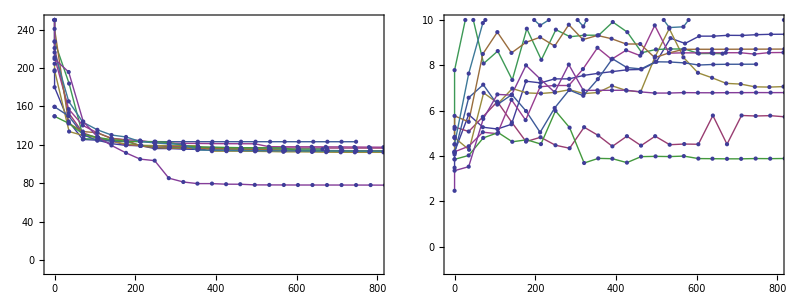

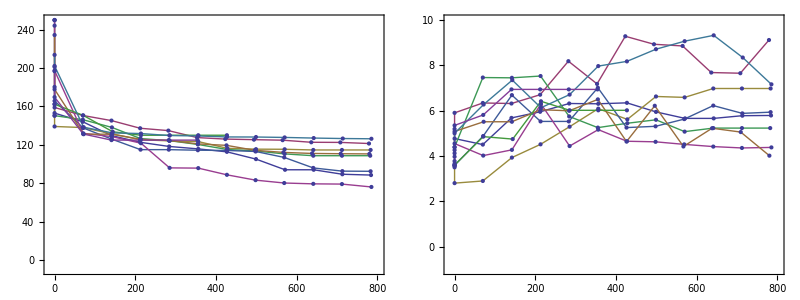

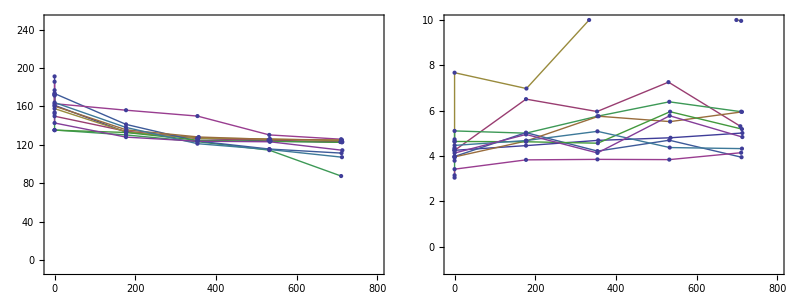

```mathematica
Vi[Import/@FN["psize/*m1p70*.dev"],P⟦1⟧]
Vi[Import/@FN["psize/*m1p140*.dev"],P⟦1⟧]
Vi[Import/@FN["psize/*m1p350*.dev"],P⟦1⟧]
```

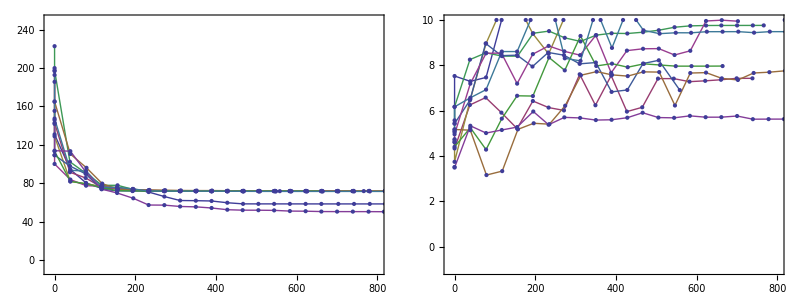

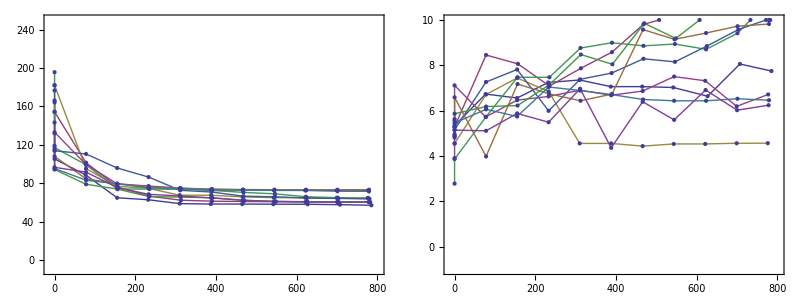

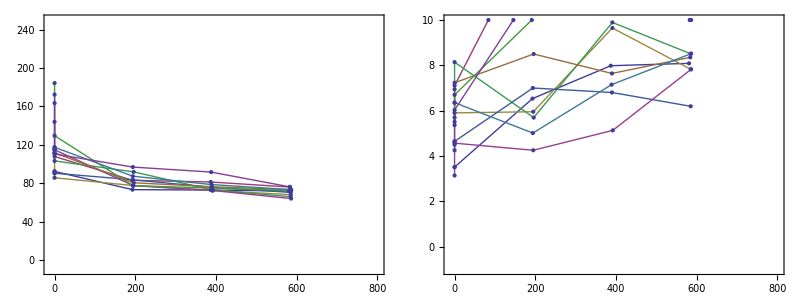

```mathematica
Vi[Import/@FN["psize/*m2p70*.dev"],P⟦2⟧]
Vi[Import/@FN["psize/*m2p140*.dev"],P⟦2⟧]
Vi[Import/@FN["psize/*m2p350*.dev"],P⟦2⟧]
```

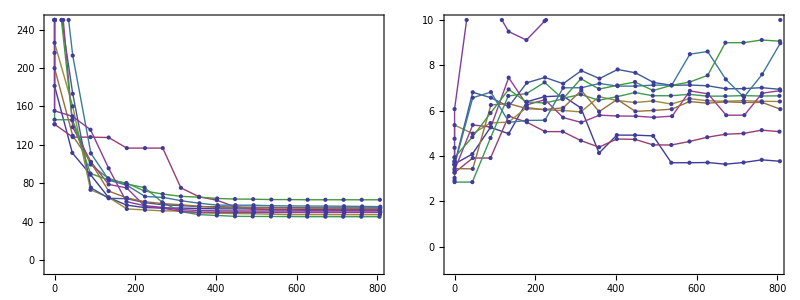

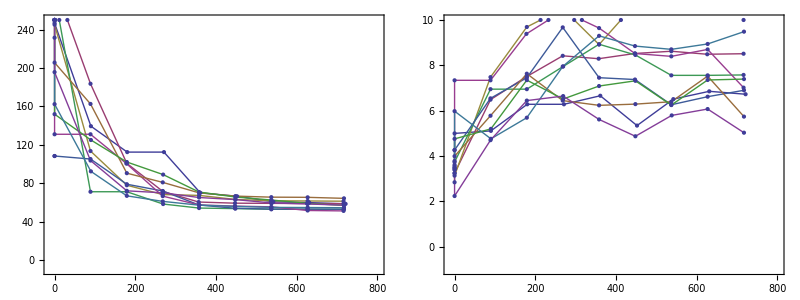

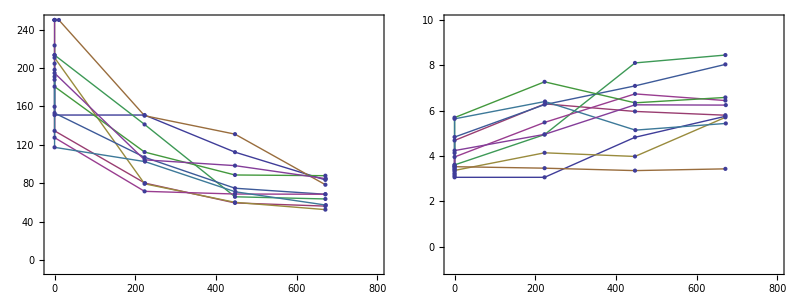

```mathematica
Vi[Import/@FN["psize/*m3p70*.dev"],P⟦3⟧]
Vi[Import/@FN["psize/*m3p140*.dev"],P⟦3⟧]
Vi[Import/@FN["psize/*m3p350*.dev"],P⟦3⟧]
```